## 1. Naloga

```mathematica
v0={10,3};
GG=9.81;
H=10;
a = {0, -GG};
x0 ={0, H};
```

```mathematica
v[t_] :={v0[[1]], v0[[2]] - GG*t};
```

v - izračuna hitrost po koordinatah x, y

```mathematica
potkx[t_]:=x0 + v0*t + a*t^2/2
```

potkx - pot ki jo opravi v danem času

```mathematica
Slikatocke[t_]:={PointSize[0.03], Point[potkx[t]]};
```

slikatocke - postavi točko, kje je žogica pri danem času

```mathematica
ClearAll[SlikaVektorja]
```

```mathematica
SlikaVektorja[t_]:=Graphics[{Arrow[{potkx[t],potkx[t]+v[t]}],Thick}, Axes->True,PlotRange->{{-1,25},{-5,15}},AspectRatio->Automatic];
```

Slikavektorja - nariše vektor iz točke ko začne žogica padati pri danem času

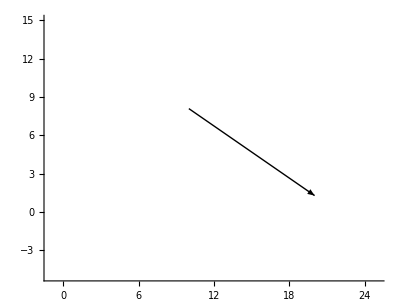

```mathematica
SlikaVektorja[1]
```

```mathematica
Manipulate[SlikaVektorja[t],{t,0,5}]
```

Čas padca žoge:

```mathematica
casPad = √((2H)/GG)
```

1.42784

Skupna hitrost in ostalo:

```mathematica
Vr=√(v0[[1]]^2 + v0[[2]]^2)
```

√109

```mathematica
casX = v0[[2]]/Vr //N
```

0.287348

```mathematica
najH=Vr^2 * casX^2 / (2 * GG) + H
```

10.4587

Čas do najvišje točke

```mathematica
casNajTocka = 2 * Vr * casX / (GG * 2)
```

0.30581

```mathematica
visina = Vr^2 * Sin[2 * ArcSin[casX]] / GG + H
```

16.1162

```mathematica
casLeta = casNajTocka * 2 + √(2 * H / GG)
```

2.03946

## 2. Naloga

```mathematica
r111=Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]]:=Hyperplane[n,v]

Format[r_Ravnina] := Graphics3D[Slika[r]]
```

-Graphics3D-

```mathematica
Normala[Ravnina[n_, v_]] := n
Tocka[Ravnina[n_, v_]] := v
```

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
```

```mathematica
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Vrne normalo kot grafični objekt Arrow

```mathematica
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
```

```mathematica
SlikaRavnin = Map[Slika, ravnine];
SlikaNormal = Map[SlikaNormale, ravnine];
Graphics3D[{SlikaRavnin, SlikaNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

## 3. Naloga

```mathematica
AA = {0,0,0};
BB = {2,3,4};
```

```mathematica
Graphics3D[Cuboid[AA,BB]]
```

-Graphics3D-